```mathematica
data=Import["G:\\GitHub Local Repository\\Mathematical-Modeling-Campus-Competition\\2020年兰州大学数学建模竞赛赛题 (1)\\Data.xlsx"];
```

```mathematica
data//Dimensions
```

{2}

```mathematica
train=data[[1,2;;All]];
```

```mathematica
test=data[[2,2;;All]];
```

```mathematica
asso=MapThread[Rule,{train[[All,1;;7]],train[[All,8]]}][[2;;All]];
```

```mathematica
model=Classify[asso,Method->"SupportVectorMachine"];
```

```mathematica
Information[model]
```

Classifier information
Data type | NumericalVector (length: 7)
Classes | ,,0.1.
Accuracy | (92.80.6) %
Method | SupportVectorMachine
Single evaluation time | 10. ms/example
Batch evaluation speed | 4.04 examples/ms
Loss | 0.26 ± 0.023
Model memory | 927. kB
Training examples used | 20000 examples
Training time | 1 4
 |

```mathematica
model[test[[2]]]
```

1.

```mathematica
features=train[[All,1;;7]];
```

```mathematica
lables=train[[All,8]];
```

```mathematica
reduced=DimensionReduce[features,2,Method->"PrincipalComponentsAnalysis"];
```

```mathematica
po1=Position[lables,x_/;x==1]//Flatten;
```

```mathematica
po2=Position[lables,x_/;x==0]//Flatten;
```

```mathematica
point1=reduced[[po1]];
```

```mathematica
point2=reduced[[po2]];
```

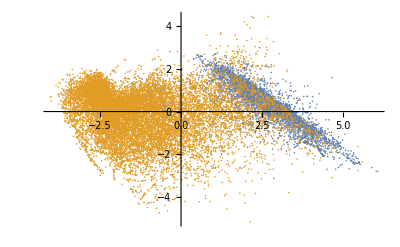

```mathematica
ListPlot[{point2,point1},PlotRange->{Full,All}]
```

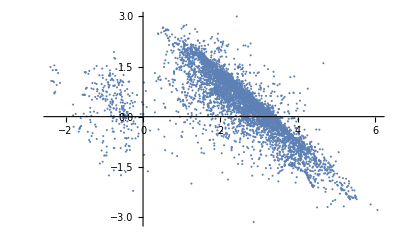

```mathematica
ListPlot[{point2},PlotRange->{Full,All}]
```

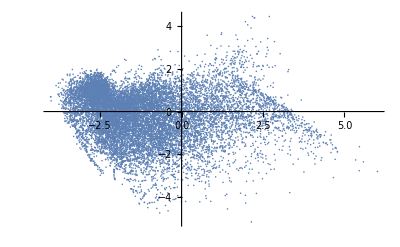

```mathematica
ListPlot[{point1},PlotRange->{Full,All}]
```

```mathematica
asso2=MapThread[Rule,{reduced,lables}];
```

```mathematica
model2=Classify[asso2,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
```

```mathematica
model2//Information
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,0.1.
Accuracy | (92.100.27) %
Method | SupportVectorMachine
Single evaluation time | 5.39 ms/example
Batch evaluation speed | 10.4 examples/ms
Loss | 0.264 ± 0.0084
Model memory | 1.02 MB
Training examples used | 20000 examples
Training time | 1 12
 |

```mathematica
clusters={point1,point2};
```

```mathematica
plota=ListPointPlot3D[Map[Append[#,1]&,clusters,{2}], PlotStyle->{Green,Red}]
```

-Graphics3D-

```mathematica
plotb=Plot3D[{
model2[{x,y},"Probability"->1.],
model2[{x,y},"Probability"->0.]
},
{x,-6,6},{y,-6,6},
 Exclusions->None]
```

-Graphics3D-

```mathematica
Show[plota,plotb,ViewPoint->Above]
```

-Graphics3D-

```mathematica
Information[model2,"FunctionProperties"]
```

{Properties,Decision,Distribution,Probabilities,LogProbabilities,ExpectedUtilities,TopProbabilities}